```mathematica
SetOptions[$FrontEnd,GlobalInitializationCellWarning -> False];
SetOptions[EvaluationNotebook[], InitializationCellEvaluation -> True, InitializationCellWarning -> False];
OpenCloseCell[name_] := Module[{nn},
nn = ButtonNotebook[]; SelectionMove[nn, All, ButtonCell]; 
    SelectionMove[nn, All, CellGroup]; FrontEndTokenExecute["OpenCloseGroup"]]
```

# Документ для выполнения задания работы “Программная реализация и сравнение вычислительной эффективности алгоритмов минимизации функций”.

В документе содержаться заготовкой для реализации метода Хука-Дживса (для простоты можно опираться на уже реализованный метод локальной вариации).
	Для отладки программы необходимо проверить ее работоспособность на простой и овражистой функциях, а также провести исследование на поиск лучшего коэффициента. После отладки для проведения сравнительной характеристики необходимо задать функцию с именем HukaJifsa и провести сравнительный анализ методов в основном документе.

#### Начальные определения и иллюстрации. ↕

Произвести вычисления в этом разделе

Входные данные :
h0 - начальный шаг поиска.
ϵ -требуемая точность.
x0 -начальная точка поиска.

```mathematica
h0={1,0.5};
x0={9.1,9.8};
ϵ=0.001;
λbest=2.5;
kolit=0;
```

Описание функции для минимизации:

```mathematica
Clear[fun,x,y];
fun[{x_,y_}]:=Module[{},kolit++;2(y-1)^2+(x-1)^2];
```

Графики иллюстрирующие функцию:

```mathematica
DenGr=DensityPlot[fun[{x,y}],{x,-10,10},{y,-10,10},Mesh-> False,PlotPoints->100];
ConGr=ContourPlot[fun[{x,y}],{x,-10,10},{y,-10,10},Contours->20];PloGr=Plot3D[fun[{x,y}],{x,-10,10},{y,-10,10}];

GraphicsGrid[{{DenGr,ConGr,PloGr}}]
```

-Graphics-

Входными параметрами функции являются:
1. Двумерный вектор.

Описание функции покоординатного поиска :

```mathematica
CoordDown[fn2_,{s1_,s2_},{h1_,h2_}]:=Module[{z,vv,fl},
vv={s1,s2};
z=fn2[vv];
fl=False;
(*Поиск уменьшения по первой координате*)
vv⟦1⟧+=Which[
z>fn2[vv+{-h1,0}],-h1,
z>fn2[vv+{h1,0}],h1,
True,0
];
z=fn2[vv];
(*Поиск уменьшения по второй координате*)
vv⟦2⟧+=Which[
z>fn2[vv+{0,-h2}],-h2,
z>fn2[vv+{0,h2}],h2,
True,0
];
vv
];
```

Входными параметрами функции являются:
1. Функция для поиска минимума.
2. Точка, из которой осуществляется поиск.
3. Шаг поиска.

#### Метод Хука-Дживса. ↕

Произвести вычисления в этом разделе

Цикл ( см.метод локальной вариации) :

Алгоритм метода Хука-Дживса

 1.Выбор начальной точки OverVector[x_0] ,h⃗ и точности поиска ϵ
 2. OverVector[x_b]=OverVector[x_0]
 3. Выполнить покоординатный поиск с шагом h⃗ из OverVector[x_b] с результатом в OverVector[x_s] 
 4. Если OverVector[x_s]=OverVector[x_b], то 
	4.1. h⃗ =(h⃗)/10. 
 4.2. Если|h⃗ |<ϵ , то (x⃗)^*=OverVector[x_s]  и завершить работу. 
	иначе перейти к 3. 
 5. OverVector[x_p] =OverVector[x_b] +λ (OverVector[x_s]-OverVector[x_b])
 6. Выполнить покоординатный поиск с шагом h⃗ из OverVector[x_p] с результатом в OverVector[x_q] 
 7. Если F^0(OverVector[x_s])≤F^0(OverVector[x_q]) , то 
	7.1. OverVector[x_b]= OverVector[x_s]
	7.2. Перейти к 3.
	иначе 
	7.3. OverVector[x_b]= OverVector[x_s]
	7.4. OverVector[x_s]= OverVector[x_q]
	7.5. Перейти к 5

Произвести вычисления в этом разделе

Начальные значения ( см.метод локальной вариации):

```mathematica
λ=2.3;
```

```mathematica
h=h0;
xb=x0;
kolit=0;

(* код программы *)
```

Выходные данные :

```mathematica
Print["Точка минимума - ",xs,
"\nМинимум функции - ",fun[xs],
"\nКоличество вызовов целевой функции - ",kolit]
```

Ответ
Точка минимума - {1.,1.}
Минимум функции - 5.57133×10^-30
Количество вызовов целевой функции - 133

Оформите метод в виде функции, имеющей приведенные аргументы и возвращающей точку минимума и количество затраченных итераций:

```mathematica
HukaJifsa[fn_,{x01_,x02_},ϵ_,{h01_,h02_},λ_]:=
Module[ {xb={x01,x02},xs,xp,xq,h={h01,h02}},
kolit=0;


{xs, kolit}
];
```

Входными параметрами функции являются:
1. Функция для поиска минимума.
2. Точка, из которой осуществляется поиск.
3. Точность поиска.
4. Начальный шаг поиска.
5. Параметр ускорения.
Выходные параметры: точка минимума и количество иттераций.

#### Поиск лучшего коэффициента. ↕

График иллюстрирующий зависимость числа вызовов целевой функции в методе от параметра λ :

```mathematica
qq={};
For[λ=1.7,λ<4,λ+=0.1,
pp=HukaJifsa[fun,x0,ϵ,h0,λ];
qq=Append[qq,{λ,pp⟦2⟧}]
];
ListPlot[qq,Joined->True]
```

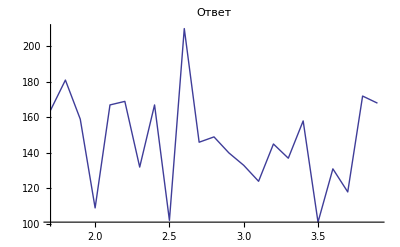

Поиск лучшего λ

```mathematica
itbest=qq[[1,2]];
λbest=qq[[1,1]];
For[i=2,i<Length[qq],i++,
If[qq[[i,2]]<itbest,
itbest=qq[[i,2]];
λbest=qq[[i,1]]
]
];λbest
```

```mathematica
3.5 - ответ
```

#### Примеры овражистых функций. ↕

Произвести вычисления в этом разделе

Функцию Розенброка :

```mathematica
Clear[fn1,x,y];
fn1[{x_,y_}]:=Module[{},kolit++;2(y-x^2)^2+(1-x)^2];
HukaJifsa[fn1,x0,ϵ,h0,λbest]
```

```mathematica
{{0.996125,0.992344},312} - ответ
```

Функция Витте и Холста :

```mathematica
Clear[fn2,x,y];
fn2[{x_,y_}]:=Module[{},kolit++;2(y-x^3)^2+(1-x)^2];
HukaJifsa[fn2,x0,ϵ,h0,λbest]
```

```mathematica
{{0.99975,0.999297},558} - ответ
```

Функция Брока :

```mathematica
Clear[fn3,x,y];
fn3[{x_,y_}]:=Module[{},kolit++;∑_(i=1)^10 ((-ⅇ^(-i/10)+ⅇ^(-(i x)/10))^2+(ⅇ^-i-ⅇ^(-(i y)/10))^2)];
HukaJifsa[fn3,x0,ϵ,h0,λbest]
```

```mathematica
{{1.,10.0002},139} - ответ
```

Функция Уайдла и Ван Ремортела :

```mathematica
Clear[fn4,x,y];
α=√3;β=2;δ=1/2;
 z1[x_,y_]=(x √3-y)/2+α √(δ/(β^2+α^2));
z2[x_,y_]=(x+y √3)/2;
fn4[{x_,y_}]:=Module[{},kolit++;-α z1[x,y]+β √(z1[x,y]^2+δ(z2[x,y]^2+1))-α √(δ/(β^2+α^2))];
HukaJifsa[fn4,x0,ϵ,h0,λbest]
```

```mathematica
{{0.66,-0.381},187} - ответ
```

Закрыть Перейти в основной документ